# SVM-BDS-BDT Comparison Results, 6/11/16

## Raw Data

## SVM: c, γ, Number of Support Vectors, False Positive Fraction, False Negative Fraction, Efficiency, Distance

```mathematica
SVMLinearHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","LinearHardTestingAll0705"}],"Table"];
SVMLinearHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","LinearHardTestingSignal0705"}],"Table"];
SVMLinearHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","LinearHardTestingBackground0705"}],"Table"];

SVMLinearSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","LinearSoftTestingAll0705"}],"Table"];
SVMLinearSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","LinearSoftTestingSignal0705"}],"Table"];
SVMLinearSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","LinearSoftTestingBackground0705"}],"Table"];


SVMCircleHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","CircleHardTestingAll0705"}],"Table"];
SVMCircleHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","CircleHardTestingSignal0705"}],"Table"];
SVMCircleHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","CircleHardTestingBackground0705"}],"Table"];

SVMCircleSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","CircleSoftTestingAll0705"}],"Table"];
SVMCircleSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","CircleSoftTestingSignal0705"}],"Table"];
SVMCircleSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","CircleSoftTestingBackground0705"}],"Table"];


SVMTwoCircleHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","TwoCircleHardTestingAll0705"}],"Table"];
SVMTwoCircleHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","TwoCircleHardTestingSignal0705"}],"Table"];
SVMTwoCircleHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","TwoCircleHardTestingBackground0705"}],"Table"];

SVMTwoCircleSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","TwoCircleSoftTestingAll0705"}],"Table"];
SVMTwoCircleSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","TwoCircleSoftTestingSignal0705"}],"Table"];
SVMTwoCircleSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"SVM","Results","TwoCircleSoftTestingBackground0705"}],"Table"];


SVMAllRawData = {SVMLinearHardTestingAllRawData,SVMLinearHardTestingSignalRawData,SVMLinearHardTestingBackgroundRawData,SVMLinearSoftTestingAllRawData,SVMLinearSoftTestingSignalRawData,SVMLinearSoftTestingBackgroundRawData,SVMCircleHardTestingAllRawData,SVMCircleHardTestingSignalRawData,SVMCircleHardTestingBackgroundRawData,SVMCircleSoftTestingAllRawData,SVMCircleSoftTestingSignalRawData,SVMCircleSoftTestingBackgroundRawData,SVMTwoCircleHardTestingAllRawData,SVMTwoCircleHardTestingSignalRawData,SVMTwoCircleHardTestingBackgroundRawData,SVMTwoCircleSoftTestingAllRawData,SVMTwoCircleSoftTestingSignalRawData,SVMTwoCircleSoftTestingBackgroundRawData};

SVMAllDataTypes={"Linear Hard Testing All","Linear Hard Testing Signal","Linear Hard Testing Background","Linear Soft Testing All","Linear Soft Testing Signal","Linear Soft Testing Background","Circle Hard Testing All","Circle Hard Testing Signal","Circle Hard Testing Background","Circle Soft Testing All","Circle Soft Testing Signal","Circle Soft Testing Background","Two Circle Hard Testing All","Two Circle Hard Testing Signal","Two Circle Hard Testing Background","Two Circle Soft Testing All","Two Circle Soft Testing Signal","Two Circle Soft Testing Background"};
```

## BDS: Number of Stumps, Efficiency, False Positive Fraction, False Negative Fraction

```mathematica
BDSLinearHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","LinearHardTestingAll0705"}],"Table"];
BDSLinearHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","LinearHardTestingSignal0705"}],"Table"];
BDSLinearHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","LinearHardTestingBackground0705"}],"Table"];

BDSLinearSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","LinearSoftTestingAll0705"}],"Table"];
BDSLinearSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","LinearSoftTestingSignal0705"}],"Table"];
BDSLinearSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","LinearSoftTestingBackground0705"}],"Table"];


BDSCircleHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","CircleHardTestingAll0705"}],"Table"];
BDSCircleHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","CircleHardTestingSignal0705"}],"Table"];
BDSCircleHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","CircleHardTestingBackground0705"}],"Table"];

BDSCircleSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","CircleSoftTestingAll0705"}],"Table"];
BDSCircleSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","CircleSoftTestingSignal0705"}],"Table"];
BDSCircleSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","CircleSoftTestingBackground0705"}],"Table"];


BDSTwoCircleHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","TwoCircleHardTestingAll0705"}],"Table"];
BDSTwoCircleHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","TwoCircleHardTestingSignal0705"}],"Table"];
BDSTwoCircleHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","TwoCircleHardTestingBackground0705"}],"Table"];

BDSTwoCircleSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","TwoCircleSoftTestingAll0705"}],"Table"];
BDSTwoCircleSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","TwoCircleSoftTestingSignal0705"}],"Table"];
BDSTwoCircleSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsStump","TwoCircleSoftTestingBackground0705"}],"Table"];


BDSAllRawData={BDSLinearHardTestingAllRawData,BDSLinearHardTestingSignalRawData,BDSLinearHardTestingBackgroundRawData,BDSLinearSoftTestingAllRawData,BDSLinearSoftTestingSignalRawData,BDSLinearSoftTestingBackgroundRawData,BDSCircleHardTestingAllRawData,BDSCircleHardTestingSignalRawData,BDSCircleHardTestingBackgroundRawData,BDSCircleSoftTestingAllRawData,BDSCircleSoftTestingSignalRawData,BDSCircleSoftTestingBackgroundRawData,BDSTwoCircleHardTestingAllRawData,BDSTwoCircleHardTestingSignalRawData,BDSTwoCircleHardTestingBackgroundRawData,BDSTwoCircleSoftTestingAllRawData,BDSTwoCircleSoftTestingSignalRawData,BDSTwoCircleSoftTestingBackgroundRawData};

BDSAllDataTypes={"Linear Hard Testing All","Linear Hard Testing Signal","Linear Hard Testing Background","Linear Soft Testing All","Linear Soft Testing Signal","Linear Soft Testing Background","Circle Hard Testing All","Circle Hard Testing Signal","Circle Hard Testing Background","Circle Soft Testing All","Circle Soft Testing Signal","Circle Soft Testing Background","Two Circle Hard Testing All","Two Circle Hard Testing Signal","Two Circle Hard Testing Background","Two Circle Soft Testing All","Two Circle Soft Testing Signal","Two Circle Soft Testing Background"};
```

## BDT: Number of Trees, Efficiency, False Positive Fraction, False Negative Fraction, Distance

```mathematica
BDTLinearHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","LinearHardTestingAll0705"}],"Table"];
BDTLinearHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","LinearHardTestingSignal0705"}],"Table"];
BDTLinearHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","LinearHardTestingBackground0705"}],"Table"];

BDTLinearSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","LinearSoftTestingAll0705"}],"Table"];
BDTLinearSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","LinearSoftTestingSignal0705"}],"Table"];
BDTLinearSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","LinearSoftTestingBackground0705"}],"Table"];


BDTCircleHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","CircleHardTestingAll0705"}],"Table"];
BDTCircleHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","CircleHardTestingSignal0705"}],"Table"];
BDTCircleHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","CircleHardTestingBackground0705"}],"Table"];

BDTCircleSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","CircleSoftTestingAll0705"}],"Table"];
BDTCircleSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","CircleSoftTestingSignal0705"}],"Table"];
BDTCircleSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","CircleSoftTestingBackground0705"}],"Table"];


BDTTwoCircleHardTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","TwoCircleHardTestingAll0705"}],"Table"];
BDTTwoCircleHardTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","TwoCircleHardTestingSignal0705"}],"Table"];
BDTTwoCircleHardTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","TwoCircleHardTestingBackground0705"}],"Table"];

BDTTwoCircleSoftTestingAllRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","TwoCircleSoftTestingAll0705"}],"Table"];
BDTTwoCircleSoftTestingSignalRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","TwoCircleSoftTestingSignal0705"}],"Table"];
BDTTwoCircleSoftTestingBackgroundRawData=Import[FileNameJoin[{NotebookDirectory[],"BDT","ResultsTree","TwoCircleSoftTestingBackground0705"}],"Table"];


BDTAllRawData={BDTLinearHardTestingAllRawData,BDTLinearHardTestingSignalRawData,BDTLinearHardTestingBackgroundRawData,BDTLinearSoftTestingAllRawData,BDTLinearSoftTestingSignalRawData,BDTLinearSoftTestingBackgroundRawData,BDTCircleHardTestingAllRawData,BDTCircleHardTestingSignalRawData,BDTCircleHardTestingBackgroundRawData,BDTCircleSoftTestingAllRawData,BDTCircleSoftTestingSignalRawData,BDTCircleSoftTestingBackgroundRawData,BDTTwoCircleHardTestingAllRawData,BDTTwoCircleHardTestingSignalRawData,BDTTwoCircleHardTestingBackgroundRawData,BDTTwoCircleSoftTestingAllRawData,BDTTwoCircleSoftTestingSignalRawData,BDTTwoCircleSoftTestingBackgroundRawData};

BDTAllDataTypes={"Linear Hard Testing All","Linear Hard Testing Signal","Linear Hard Testing Background","Linear Soft Testing All","Linear Soft Testing Signal","Linear Soft Testing Background","Circle Hard Testing All","Circle Hard Testing Signal","Circle Hard Testing Background","Circle Soft Testing All","Circle Soft Testing Signal","Circle Soft Testing Background","Two Circle Hard Testing All","Two Circle Hard Testing Signal","Two Circle Hard Testing Background","Two Circle Soft Testing All","Two Circle Soft Testing Signal","Two Circle Soft Testing Background"};
```

## Formatted Datasets

## SVM

### c-γ-Efficiency

```mathematica
SVMCGE[RawData_]:=RawData[[All,{1,2, 6}]]
```

### Log(c)-γ-Efficiency

```mathematica
SVMLogCGE[RawData_]:=MapAt[Log10, RawData[[All,{1,2, 6}]], {All, 1}]
```

### c-γ-Distance

```mathematica
SVMCGD[RawData_]:=RawData[[All,{1,2, 7}]]
```

### Log(c)-γ-Distance

```mathematica
SVMLogCGD[RawData_]:=MapAt[Log10, RawData[[All,{1,2, 7}]], {All, 1}]
```

### Efficiency-1 - False Positive Fraction

```mathematica
SVMEFP[RawData_]:= MapAt[1-#&,RawData[[All,{6,4}]],{All,2}]
```

### Efficiency-1 - False Negative Fraction

```mathematica
SVMEFN[RawData_]:= MapAt[1-#&,RawData[[All,{6,5}]],{All,2}]
```

### False Positive Fraction-Efficiency

```mathematica
SVMFPE[RawData_]:= RawData[[All,{4,6}]]
```

## BDS

### Number of Stumps-Efficiency

```mathematica
BDSSE[RawData_]:=RawData[[All,{1,2}]]
```

### Number of Stumps-Distance

```mathematica
BDSSD[RawData_]:=RawData[[All,{1,5}]]
```

### Efficiency-1 - False Positive Fraction

```mathematica
BDSEFP[RawData_]:= MapAt[1-#&,RawData[[All,{2,3}]],{All,2}]
```

### Efficiency-1 - False Negative Fraction

```mathematica
BDSEFN[RawData_]:= MapAt[1-#&,RawData[[All,{2,4}]],{All,2}]
```

### False Positive Fraction-Efficiency

```mathematica
BDSFPE[RawData_]:= RawData[[All,{3,2}]]
```

## BDT

### Number of Trees-Efficiency

```mathematica
BDTTE[RawData_]:=RawData[[All,{1,2}]]
```

### Number of Trees-Distance

```mathematica
BDTTD[RawData_]:=RawData[[All,{1,5}]]
```

### Efficiency-1 - False Positive Fraction

```mathematica
BDTEFP[RawData_]:= MapAt[1-#&,RawData[[All,{2,3}]],{All,2}]
```

### Efficiency-1 - False Negative Fraction

```mathematica
BDTEFN[RawData_]:= MapAt[1-#&,RawData[[All,{2,4}]],{All,2}]
```

### False Positive Fraction-Efficiency

```mathematica
BDTFPE[RawData_]:= RawData[[All,{3,2}]]
```

## Optimizing Parameters

## SVM

```mathematica
SVMBest[RawData_]:=First[SortBy[RawData[[All,{1,2, 6,5,7}]],Last]];
SVMBestResultTable=Grid[{{"Data Set","c","γ","Efficiency","False Negative Fraction","Distance"},Prepend[SVMBest[SVMLinearHardTestingAllRawData],"Linear Hard Testing All"],Prepend[SVMBest[SVMLinearHardTestingSignalRawData],"Linear Hard Testing Signal"],Prepend[SVMBest[SVMLinearHardTestingBackgroundRawData],"Linear Hard Testing Background"],Prepend[SVMBest[SVMLinearSoftTestingAllRawData],"Linear Soft Testing All"],Prepend[SVMBest[SVMLinearSoftTestingSignalRawData],"Linear Soft Testing Signal"],Prepend[SVMBest[SVMLinearSoftTestingBackgroundRawData],"Linear Soft Testing Background"],Prepend[SVMBest[SVMCircleHardTestingAllRawData],"Circle Hard Testing All"],Prepend[SVMBest[SVMCircleHardTestingSignalRawData],"Circle Hard Testing Signal"],Prepend[SVMBest[SVMCircleHardTestingBackgroundRawData],"Circle Hard Testing Background"],Prepend[SVMBest[SVMCircleSoftTestingAllRawData],"Circle Soft Testing All"],Prepend[SVMBest[SVMCircleSoftTestingSignalRawData],"Circle Soft Testing Signal"],Prepend[SVMBest[SVMCircleSoftTestingBackgroundRawData],"Circle Soft Testing Background"],Prepend[SVMBest[SVMTwoCircleHardTestingAllRawData],"Two Circle Hard Testing All"],Prepend[SVMBest[SVMTwoCircleHardTestingSignalRawData],"Two Circle Hard Testing Signal"],Prepend[SVMBest[SVMTwoCircleHardTestingBackgroundRawData],"Two Circle Hard Testing Background"],Prepend[SVMBest[SVMTwoCircleSoftTestingAllRawData],"Two Circle Soft Testing All"],Prepend[SVMBest[SVMTwoCircleSoftTestingSignalRawData],"Two Circle Soft Testing Signal"],Prepend[SVMBest[SVMTwoCircleSoftTestingBackgroundRawData],"Two Circle Soft Testing Background"]},Frame->All];
```

## BDS

```mathematica
BDSBest[RawData_]:=First[SortBy[RawData[[All,{1,2, 4,5}]],Last]];
BDSBestResultTable=Grid[{{"Data Set","Number of Trees","Efficiency","False Negative Fraction","Distance"},Prepend[BDSBest[BDSLinearHardTestingAllRawData],"Linear Hard Testing All"],Prepend[BDSBest[BDSLinearHardTestingSignalRawData],"Linear Hard Testing Signal"],Prepend[BDSBest[BDSLinearHardTestingBackgroundRawData],"Linear Hard Testing Background"],Prepend[BDSBest[BDSLinearSoftTestingAllRawData],"Linear Soft Testing All"],Prepend[BDSBest[BDSLinearSoftTestingSignalRawData],"Linear Soft Testing Signal"],Prepend[BDSBest[BDSLinearSoftTestingBackgroundRawData],"Linear Soft Testing Background"],Prepend[BDSBest[BDSCircleHardTestingAllRawData],"Circle Hard Testing All"],Prepend[BDSBest[BDSCircleHardTestingSignalRawData],"Circle Hard Testing Signal"],Prepend[BDSBest[BDSCircleHardTestingBackgroundRawData],"Circle Hard Testing Background"],Prepend[BDSBest[BDSCircleSoftTestingAllRawData],"Circle Soft Testing All"],Prepend[BDSBest[BDSCircleSoftTestingSignalRawData],"Circle Soft Testing Signal"],Prepend[BDSBest[BDSCircleSoftTestingBackgroundRawData],"Circle Soft Testing Background"],Prepend[BDSBest[BDSTwoCircleHardTestingAllRawData],"Two Circle Hard Testing All"],Prepend[BDSBest[BDSTwoCircleHardTestingSignalRawData],"Two Circle Hard Testing Signal"],Prepend[BDSBest[BDSTwoCircleHardTestingBackgroundRawData],"Two Circle Hard Testing Background"],Prepend[BDSBest[BDSTwoCircleSoftTestingAllRawData],"Two Circle Soft Testing All"],Prepend[BDSBest[BDSTwoCircleSoftTestingSignalRawData],"Two Circle Soft Testing Signal"],Prepend[BDSBest[BDSTwoCircleSoftTestingBackgroundRawData],"Two Circle Soft Testing Background"]},Frame->All];
```

## BDT

```mathematica
BDTBest[RawData_]:=First[SortBy[RawData[[All,{1,2, 4,5}]],Last]];
BDTBestResultTable=Grid[{{"Data Set","Number of Trees","Efficiency","False Negative Fraction","Distance"},Prepend[BDTBest[BDTLinearHardTestingAllRawData],"Linear Hard Testing All"],Prepend[BDTBest[BDTLinearHardTestingSignalRawData],"Linear Hard Testing Signal"],Prepend[BDTBest[BDTLinearHardTestingBackgroundRawData],"Linear Hard Testing Background"],Prepend[BDTBest[BDTLinearSoftTestingAllRawData],"Linear Soft Testing All"],Prepend[BDTBest[BDTLinearSoftTestingSignalRawData],"Linear Soft Testing Signal"],Prepend[BDTBest[BDTLinearSoftTestingBackgroundRawData],"Linear Soft Testing Background"],Prepend[BDTBest[BDTCircleHardTestingAllRawData],"Circle Hard Testing All"],Prepend[BDTBest[BDTCircleHardTestingSignalRawData],"Circle Hard Testing Signal"],Prepend[BDTBest[BDTCircleHardTestingBackgroundRawData],"Circle Hard Testing Background"],Prepend[BDTBest[BDTCircleSoftTestingAllRawData],"Circle Soft Testing All"],Prepend[BDTBest[BDTCircleSoftTestingSignalRawData],"Circle Soft Testing Signal"],Prepend[BDTBest[BDTCircleSoftTestingBackgroundRawData],"Circle Soft Testing Background"],Prepend[BDTBest[BDTTwoCircleHardTestingAllRawData],"Two Circle Hard Testing All"],Prepend[BDTBest[BDTTwoCircleHardTestingSignalRawData],"Two Circle Hard Testing Signal"],Prepend[BDTBest[BDTTwoCircleHardTestingBackgroundRawData],"Two Circle Hard Testing Background"],Prepend[BDTBest[BDTTwoCircleSoftTestingAllRawData],"Two Circle Soft Testing All"],Prepend[BDTBest[BDTTwoCircleSoftTestingSignalRawData],"Two Circle Soft Testing Signal"],Prepend[BDTBest[BDTTwoCircleSoftTestingBackgroundRawData],"Two Circle Soft Testing Background"]},Frame->All];
```

## Developing Plots

## SVM

### c-γ-Efficiency

```mathematica
SVMCGEPlot[RawData_,DataType_]:=ListPlot3D[SVMCGE[RawData], AxesLabel->{c, γ, Efficiency}, PlotLabel->StringJoin["SVM ",DataType," c-γ-Efficiency"],PlotStyle->Green]
```

### Log(c)-γ-Efficiency

```mathematica
SVMLogCGEPlot[RawData_,DataType_]:=ListPlot3D[SVMLogCGE[RawData], AxesLabel->{c, γ, Efficiency}, PlotLabel->StringJoin["SVM ",DataType," Log(c)-γ-Efficiency"],PlotStyle->Green]
```

### c-γ-Distance

```mathematica
SVMCGDPlot[RawData_,DataType_]:=ListPlot3D[SVMCGD[RawData], AxesLabel->{c, γ, Distance}, PlotLabel->StringJoin["SVM ",DataType," c-γ-Distance"],PlotStyle->Green]
```

### Log(c)-γ-Distance

```mathematica
SVMLogCGDPlot[RawData_,DataType_]:=ListPlot3D[SVMLogCGD[RawData], AxesLabel->{c, γ, Distance}, PlotLabel->StringJoin["SVM ",DataType," Log(c)-γ-Distance"],PlotStyle->Green]
```

### Efficiency-(1- False Positive Fraction)

```mathematica
SVMEFPPlot[RawData_,DataType_]:=ListPlot[SVMEFP[RawData], AxesLabel->{Efficiency,"1 - False Positive Fraction"}, PlotLabel->StringJoin["SVM ",DataType," Efficiency-1 - False Positive Fraction"],PlotStyle->Darker[Green]]
```

### Efficiency-(1-False Negative Fraction)

```mathematica
SVMEFNPlot[RawData_,DataType_]:=ListPlot[SVMEFN[RawData], AxesLabel->{Efficiency,"1 - False Negative Fraction"}, PlotLabel->StringJoin["SVM ",DataType," Efficiency-1 - False Negative Fraction"],PlotStyle->Darker[Green]]
```

### False Positive Fraction-Efficiency

```mathematica
SVMFPEPlot[RawData_,DataType_]:=ListPlot[SVMFPE[RawData], AxesLabel->{"False Positive Fraction",Efficiency}, PlotLabel->StringJoin["SVM ",DataType," False Positive Fraction-Efficiency"],PlotStyle->Darker[Green]]
```

## BDS

### Number of Stumps-Efficiency

```mathematica
BDSSEPlot[RawData_,DataType_]:=ListPlot[BDSSE[RawData],AxesLabel->{"Number of Stumps",Efficiency},PlotLabel->StringJoin["BDS ",DataType," Number of Stumps-Efficiency"],PlotStyle->Red]
```

### Number of Stumps-Distance

```mathematica
BDSSDPlot[RawData_,DataType_]:=ListPlot[BDSSD[RawData],AxesLabel->{"Number of Stumps",Distance},PlotLabel->StringJoin["BDS ",DataType," Number of Stumps-Distance"],PlotStyle->Red]
```

### Efficiency-(1 - False Positive Fraction)

```mathematica
BDSEFPPlot[RawData_,DataType_]:=ListPlot[BDSEFN[RawData],AxesLabel->{Efficiency,"1 - False Positive Fraction"},PlotLabel->StringJoin["BDS ",DataType," Efficiency-1 - False Positive Fraction"],PlotStyle->Red]
```

### Efficiency-(1 - False Negative Fraction)

```mathematica
BDSEFNPlot[RawData_,DataType_]:=ListPlot[BDSEFN[RawData],AxesLabel->{Efficiency,"1 - False Negative Fraction"},PlotLabel->StringJoin["BDS ",DataType," Efficiency-1 - False Negative Fraction"],PlotStyle->Red]
```

### False Positive Fraction-Efficiency

```mathematica
BDSFPEPlot[RawData_,DataType_]:=ListPlot[BDSFPE[RawData],AxesLabel->{"False Positive Fraction",Efficiency},PlotLabel->StringJoin["BDS ",DataType," False Positive Fraction-Efficiency"],PlotStyle->Red]
```

## BDT

### Number of Trees-Efficiency

```mathematica
BDTTEPlot[RawData_,DataType_]:=ListPlot[BDTTE[RawData],AxesLabel->{"Number of Trees",Efficiency},PlotLabel->StringJoin["BDT ",DataType," Number of Trees-Efficiency"],PlotStyle->Blue]
```

### Number of Trees-Distance

```mathematica
BDTTDPlot[RawData_,DataType_]:=ListPlot[BDTTD[RawData],AxesLabel->{"Number of Trees",Distance},PlotLabel->StringJoin["BDT ",DataType," Number of Trees-Distance"],PlotStyle->Blue]
```

### Efficiency-(1 - False Positive Fraction)

```mathematica
BDTEFPPlot[RawData_,DataType_]:=ListPlot[BDTEFN[RawData],AxesLabel->{Efficiency,"1 - False Positive Fraction"},PlotLabel->StringJoin["BDT ",DataType," Efficiency-1 - False Positive Fraction"],PlotStyle->Blue]
```

### Efficiency-(1 - False Negative Fraction)

```mathematica
BDTEFNPlot[RawData_,DataType_]:=ListPlot[BDTEFN[RawData],AxesLabel->{Efficiency,"1 - False Negative Fraction"},PlotLabel->StringJoin["BDT ",DataType," Efficiency-1 - False Negative Fraction"],PlotStyle->Blue]
```

### False Positive Fraction-Efficiency

```mathematica
BDTFPEPlot[RawData_,DataType_]:=ListPlot[BDTFPE[RawData],AxesLabel->{"False Positive Fraction",Efficiency},PlotLabel->StringJoin["BDT ",DataType," False Positive Fraction-Efficiency"],PlotStyle->Blue]
```

## All

```mathematica
AllPlots[PlotType_,AllRawData_,AllDataTypes_]:=Block[{},
For[i = 1, i ≤ Length[AllRawData],i++,
PlotType[AllRawData[i],AllDataTypes[i]]
]
]
```

## Visualizing Results

## Optimized Parameters

### SVM

```mathematica
SVMBestResultTable
```

Data Set | c | γ | Efficiency | False Negative Fraction | Distance
Linear Hard Testing All | 100. | 1.5 | 0.999599 | 0.000400818 | 0.000466927
Linear Hard Testing Signal | 100. | 1. | 0.999599 | 0.000400818 | 0.000400818
Linear Hard Testing Background | 0.001 | 3.5 | 1 | 0 | 0.
Linear Soft Testing All | 0.00316228 | 1. | 0.970041 | 0.0299594 | 0.0416965
Linear Soft Testing Signal | 0.001 | 1. | 0.970281 | 0.0297194 | 0.0297194
Linear Soft Testing Background | 0.001 | 6. | 1 | 0 | 0.
Circle Hard Testing All | 56.2341 | 1. | 0.999036 | 0.000964475 | 0.00102353
Circle Hard Testing Signal | 56.2341 | 1. | 0.999036 | 0.000964475 | 0.000964475
Circle Hard Testing Background | 0.001 | 1.5 | 1 | 0 | 0.
Circle Soft Testing All | 10. | 1. | 0.960594 | 0.0394065 | 0.040742
Circle Soft Testing Signal | 10. | 1. | 0.960594 | 0.0394065 | 0.0394065
Circle Soft Testing Background | 0.001 | 2.5 | 1 | 0 | 0.
Two Circle Hard Testing All | 31.6228 | 1. | 0.99916 | 0.00084016 | 0.00115362
Two Circle Hard Testing Signal | 31.6228 | 1. | 0.99916 | 0.00084016 | 0.00084016
Two Circle Hard Testing Background | 0.001 | 2. | 1 | 0 | 0.
Two Circle Soft Testing All | 100. | 1. | 0.955292 | 0.0447078 | 0.0474026
Two Circle Soft Testing Signal | 100. | 1. | 0.955292 | 0.0447078 | 0.0447078
Two Circle Soft Testing Background | 0.001 | 3. | 1 | 0 | 0.

### BDS

```mathematica
BDSBestResultTable
```

Data Set | Number of Trees | Efficiency | False Negative Fraction | Distance
Linear Hard Testing All | 970 | 0.99764 | 0.00236 | 0.00321279
Linear Hard Testing Signal | 570 | 0.99783 | 0.00217 | 0.00217
Linear Hard Testing Background | 420 | 1. | 0. | 0.00212
Linear Soft Testing All | 250 | 0.98156 | 0.01844 | 0.025429
Linear Soft Testing Signal | 310 | 0.98214 | 0.01786 | 0.01786
Linear Soft Testing Background | 70 | 1. | 0. | 0.0168
Circle Hard Testing All | 1000 | 0.99956 | 0.00044 | 0.00209669
Circle Hard Testing Signal | 200 | 0.99993 | 0.00007 | 0.00007
Circle Hard Testing Background | 1000 | 1. | 0. | 0.00205
Circle Soft Testing All | 890 | 0.99503 | 0.00497 | 0.0118614
Circle Soft Testing Signal | 10 | 0.99825 | 0.00175 | 0.00175
Circle Soft Testing Background | 860 | 1. | 0. | 0.01075
Two Circle Hard Testing All | 40 | 0.92048 | 0.07952 | 0.0809279
Two Circle Hard Testing Signal | 40 | 0.92048 | 0.07952 | 0.07952
Two Circle Hard Testing Background | 10 | 1. | 0. | 0.
Two Circle Soft Testing All | 40 | 0.91296 | 0.08704 | 0.0888676
Two Circle Soft Testing Signal | 40 | 0.91296 | 0.08704 | 0.08704
Two Circle Soft Testing Background | 10 | 1. | 0. | 0.

### BDT

```mathematica
BDTBestResultTable
```

Data Set | Number of Trees | Efficiency | False Negative Fraction | Distance
Linear Hard Testing All | 10 | 0.9989 | 0.0011 | 0.00165759
Linear Hard Testing Signal | 10 | 0.9989 | 0.0011 | 0.0011
Linear Hard Testing Background | 30 | 1. | 0. | 0.00104
Linear Soft Testing All | 120 | 0.97995 | 0.02005 | 0.0281928
Linear Soft Testing Signal | 30 | 0.97995 | 0.02005 | 0.02005
Linear Soft Testing Background | 600 | 1. | 0. | 0.01964
Circle Hard Testing All | 50 | 0.99938 | 0.00062 | 0.000988585
Circle Hard Testing Signal | 50 | 0.99938 | 0.00062 | 0.00062
Circle Hard Testing Background | 80 | 1. | 0. | 0.00075
Circle Soft Testing All | 830 | 0.99214 | 0.00786 | 0.0119641
Circle Soft Testing Signal | 490 | 0.99216 | 0.00784 | 0.00784
Circle Soft Testing Background | 680 | 1. | 0. | 0.00898
Two Circle Hard Testing All | 30 | 0.99885 | 0.00115 | 0.00161227
Two Circle Hard Testing Signal | 30 | 0.99885 | 0.00115 | 0.00115
Two Circle Hard Testing Background | 20 | 1. | 0. | 0.00112
Two Circle Soft Testing All | 530 | 0.98749 | 0.01251 | 0.0193407
Two Circle Soft Testing Signal | 550 | 0.98756 | 0.01244 | 0.01244
Two Circle Soft Testing Background | 90 | 1. | 0. | 0.01473

## Plots

#### c-γ-Efficiency

```mathematica
AllPlots[SVMCGEPlot,SVMAllRawData,SVMAllDataTypes]
```

Part::partd: Part specification {{{0.001, 1., 48591, 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436, 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080, 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373, 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, « 16 », {« 1 »}}[1] ⟦ All, {1, 2, 6} ⟧ is longer than depth of object.

StringJoin::string: String expected at position 2 in "SVM " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", "Circle Hard Testing All", « 5 », "Two Circle Hard Testing All", "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[1] <> " c-\[Gamma]-Efficiency".

Part::partd: Part specification {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {« 1 »}, « 14 », {« 1 »}, {{« 1 »}, « 49 », « 181 »}}[« 6 »] ⟦ « 1 » ⟧ is longer than depth of object.

Part::partd: Part specification {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {« 1 »}, {« 1 »}, {« 1 »}, « 10 », {« 1 »}, {« 1 »}, {« 1 »}, {« 1 »}}[1.] ⟦ « 1 » ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ListPlot3D::arrayerr: {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {« 1 »}, {« 1 »}, {« 1 »}, « 10 », {« 1 »}, {« 1 »}, {« 1 »}, {« 1 »}}[1.] ⟦ « 1 » ⟧ must be a valid array or a list of valid arrays.

StringJoin::string: String expected at position 2 in "SVM " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", "Circle Hard Testing All", « 5 », "Two Circle Hard Testing All", "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[2] <> " c-\[Gamma]-Efficiency".

ListPlot3D::arrayerr: {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {« 1 »}, {« 1 »}, {« 1 »}, « 10 », {« 1 »}, {« 1 »}, {« 1 »}, {« 1 »}}[2.] ⟦ « 1 » ⟧ must be a valid array or a list of valid arrays.

StringJoin::string: String expected at position 2 in "SVM " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", "Circle Hard Testing All", « 5 », "Two Circle Hard Testing All", "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[3] <> " c-\[Gamma]-Efficiency".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

ListPlot3D::arrayerr: {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {« 1 »}, {« 1 »}, {« 1 »}, « 10 », {« 1 »}, {« 1 »}, {« 1 »}, {« 1 »}}[3.] ⟦ « 1 » ⟧ must be a valid array or a list of valid arrays.

General::stop: Further output of ListPlot3D :: arrayerr will be suppressed during this calculation.

#### Log(c)-γ-Efficiency

```mathematica
AllPlots[SVMLogCGEPlot,SVMAllRawData,SVMAllDataTypes]
```

Part::partd: Part specification {{{0.001, 1., 48591, 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436, 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080, 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373, 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, « 16 », {« 1 »}}[1] ⟦ All, {1, 2, 6} ⟧ is longer than depth of object.

MapAt::partw: Part {All, 1} of {{{0.001, 1., 48591, 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436, 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080, 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373, 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, « 16 », {« 1 »}}[1] ⟦ All, {1, 2, 6} ⟧ does not exist.

StringJoin::string: String expected at position 2 in "SVM " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 6 », "Two Circle Hard Testing All", "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[1] <> " Log(c)-\[Gamma]-Efficiency".

Part::partd: Part specification {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {« 1 »}, « 14 », {« 1 »}, {{« 1 »}, « 49 », « 181 »}}[« 6 »] ⟦ « 1 » ⟧ is longer than depth of object.

MapAt::partw: Part {All, 1.} of {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {« 1 »}, « 14 », {« 1 »}, {{« 1 »}, « 49 », « 181 »}}[« 6 »] ⟦ « 1 » ⟧ does not exist.

Part::partd: Part specification {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {« 1 »}, {« 1 »}, {« 1 »}, « 10 », {« 1 »}, {« 1 »}, {« 1 »}, {« 1 »}}[1.] ⟦ « 1 » ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

MapAt::partw: Part {All, 1.} of {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {« 1 »}, {« 1 »}, {« 1 »}, « 10 », {« 1 »}, {« 1 »}, {« 1 »}, {« 1 »}}[1.] ⟦ « 1 » ⟧ does not exist.

General::stop: Further output of MapAt :: partw will be suppressed during this calculation.

ListPlot3D::arrayerr: MapAt[Log10, {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {{« 1 »}, « 50 »}, « 15 », {« 1 »}}[1.] ⟦ « 1 » ⟧, {All, 1.}] must be a valid array or a list of valid arrays.

StringJoin::string: String expected at position 2 in "SVM " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 6 », "Two Circle Hard Testing All", "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[2] <> " Log(c)-\[Gamma]-Efficiency".

ListPlot3D::arrayerr: MapAt[Log10, {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {{« 1 »}, « 50 »}, « 15 », {« 1 »}}[2.] ⟦ « 1 » ⟧, {All, 1.}] must be a valid array or a list of valid arrays.

StringJoin::string: String expected at position 2 in "SVM " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 6 », "Two Circle Hard Testing All", "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[3] <> " Log(c)-\[Gamma]-Efficiency".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

ListPlot3D::arrayerr: MapAt[Log10, {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {{« 1 »}, « 50 »}, « 15 », {« 1 »}}[3.] ⟦ « 1 » ⟧, {All, 1.}] must be a valid array or a list of valid arrays.

General::stop: Further output of ListPlot3D :: arrayerr will be suppressed during this calculation.

#### c-γ-Distance

```mathematica
AllPlots[SVMCGDPlot,SVMAllRawData,SVMAllDataTypes]
```

Part::partd: Part specification {{{0.001, 1., 48591, 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436, 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080, 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373, 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, « 16 », {« 1 »}}[1] ⟦ All, {1, 2, 7} ⟧ is longer than depth of object.

StringJoin::string: String expected at position 2 in "SVM " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 6 », "Two Circle Hard Testing All", "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[1] <> " c-\[Gamma]-Distance".

Part::partd: Part specification {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {« 1 »}, « 14 », {« 1 »}, {{« 1 »}, « 49 », « 181 »}}[« 6 »] ⟦ « 1 » ⟧ is longer than depth of object.

Part::partd: Part specification {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {« 1 »}, {« 1 »}, {« 1 »}, « 10 », {« 1 »}, {« 1 »}, {« 1 »}, {« 1 »}}[1.] ⟦ « 1 » ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ListPlot3D::arrayerr: {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {« 1 »}, {« 1 »}, {« 1 »}, « 10 », {« 1 »}, {« 1 »}, {« 1 »}, {« 1 »}}[1.] ⟦ « 1 » ⟧ must be a valid array or a list of valid arrays.

StringJoin::string: String expected at position 2 in "SVM " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 6 », "Two Circle Hard Testing All", "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[2] <> " c-\[Gamma]-Distance".

ListPlot3D::arrayerr: {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {« 1 »}, {« 1 »}, {« 1 »}, « 10 », {« 1 »}, {« 1 »}, {« 1 »}, {« 1 »}}[2.] ⟦ « 1 » ⟧ must be a valid array or a list of valid arrays.

StringJoin::string: String expected at position 2 in "SVM " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 6 », "Two Circle Hard Testing All", "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[3] <> " c-\[Gamma]-Distance".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

ListPlot3D::arrayerr: {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {« 1 »}, {« 1 »}, {« 1 »}, « 10 », {« 1 »}, {« 1 »}, {« 1 »}, {« 1 »}}[3.] ⟦ « 1 » ⟧ must be a valid array or a list of valid arrays.

General::stop: Further output of ListPlot3D :: arrayerr will be suppressed during this calculation.

#### Log(c)-γ-Distance

```mathematica
AllPlots[SVMLogCGDPlot,SVMAllRawData,SVMAllDataTypes]
```

Part::partd: Part specification {{{0.001, 1., 48591, 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436, 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080, 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373, 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, « 16 », {« 1 »}}[1] ⟦ All, {1, 2, 7} ⟧ is longer than depth of object.

MapAt::partw: Part {All, 1} of {{{0.001, 1., 48591, 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436, 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080, 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373, 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, « 16 », {« 1 »}}[1] ⟦ All, {1, 2, 7} ⟧ does not exist.

StringJoin::string: String expected at position 2 in "SVM " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 6 », "Two Circle Hard Testing All", "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[1] <> " Log(c)-\[Gamma]-Distance".

Part::partd: Part specification {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {« 1 »}, « 14 », {« 1 »}, {{« 1 »}, « 49 », « 181 »}}[« 6 »] ⟦ « 1 » ⟧ is longer than depth of object.

MapAt::partw: Part {All, 1.} of {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {« 1 »}, « 14 », {« 1 »}, {{« 1 »}, « 49 », « 181 »}}[« 6 »] ⟦ « 1 » ⟧ does not exist.

Part::partd: Part specification {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {« 1 »}, {« 1 »}, {« 1 »}, « 10 », {« 1 »}, {« 1 »}, {« 1 »}, {« 1 »}}[1.] ⟦ « 1 » ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

MapAt::partw: Part {All, 1.} of {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {« 1 »}, {« 1 »}, {« 1 »}, « 10 », {« 1 »}, {« 1 »}, {« 1 »}, {« 1 »}}[1.] ⟦ « 1 » ⟧ does not exist.

General::stop: Further output of MapAt :: partw will be suppressed during this calculation.

ListPlot3D::arrayerr: MapAt[Log10, {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {{« 1 »}, « 50 »}, « 15 », {« 1 »}}[1.] ⟦ « 1 » ⟧, {All, 1.}] must be a valid array or a list of valid arrays.

StringJoin::string: String expected at position 2 in "SVM " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 6 », "Two Circle Hard Testing All", "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[2] <> " Log(c)-\[Gamma]-Distance".

ListPlot3D::arrayerr: MapAt[Log10, {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {{« 1 »}, « 50 »}, « 15 », {« 1 »}}[2.] ⟦ « 1 » ⟧, {All, 1.}] must be a valid array or a list of valid arrays.

StringJoin::string: String expected at position 2 in "SVM " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 6 », "Two Circle Hard Testing All", "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[3] <> " Log(c)-\[Gamma]-Distance".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

ListPlot3D::arrayerr: MapAt[Log10, {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {{« 1 »}, « 50 »}, « 15 », {« 1 »}}[3.] ⟦ « 1 » ⟧, {All, 1.}] must be a valid array or a list of valid arrays.

General::stop: Further output of ListPlot3D :: arrayerr will be suppressed during this calculation.

#### Efficiency-(1- False Positive Fraction)

```mathematica
AllPlots[SVMEFPPlot,SVMAllRawData,SVMAllDataTypes]
```

Part::partd: Part specification {{{0.001, 1., 48591, 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436, 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080, 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373, 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, « 16 », {« 1 »}}[1] ⟦ All, {6, 4} ⟧ is longer than depth of object.

MapAt::partw: Part {All, 2} of {{{0.001, 1., 48591, 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436, 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080, 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373, 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, « 16 », {« 1 »}}[1] ⟦ All, {6, 4} ⟧ does not exist.

StringJoin::string: String expected at position 2 in "SVM " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 7 », "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[1] <> " Efficiency-1 - False Positive Fraction".

Part::partd: Part specification {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {« 1 »}, « 14 », {« 1 »}, {{« 1 »}, « 49 », « 181 »}}[« 6 »] ⟦ « 1 » ⟧ is longer than depth of object.

MapAt::partw: Part 2 of {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, « 16 », {« 1 »}}[1.] does not exist.

Part::partd: Part specification {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {« 1 »}, {« 1 »}, {« 1 »}, « 10 », {« 1 »}, {« 1 »}, {« 1 »}, {« 1 »}}[1.] ⟦ « 1 » ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

MapAt::partw: Part 2 of {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, « 16 », {{0.001, 1., « 3 », 1., 0.00707313}, « 50 »}}[1.] does not exist.

General::stop: Further output of MapAt :: partw will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, « 16 », {{« 1 »}, « 50 »}}[1.] ⟦ « 1 » ⟧, {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in "SVM " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 7 », "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[2] <> " Efficiency-1 - False Positive Fraction".

StringJoin::string: String expected at position 2 in "SVM " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 7 », "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[3] <> " Efficiency-1 - False Positive Fraction".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

#### Efficiency-(1 - False Negative Fraction)

```mathematica
AllPlots[SVMEFNPlot,SVMAllRawData,SVMAllDataTypes]
```

Part::partd: Part specification {{{0.001, 1., 48591, 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436, 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080, 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373, 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, « 16 », {« 1 »}}[1] ⟦ All, {6, 5} ⟧ is longer than depth of object.

MapAt::partw: Part {All, 2} of {{{0.001, 1., 48591, 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436, 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080, 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373, 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, « 16 », {« 1 »}}[1] ⟦ All, {6, 5} ⟧ does not exist.

StringJoin::string: String expected at position 2 in "SVM " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 7 », "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[1] <> " Efficiency-1 - False Negative Fraction".

Part::partd: Part specification {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {« 1 »}, « 14 », {« 1 »}, {{« 1 »}, « 49 », « 181 »}}[« 6 »] ⟦ « 1 » ⟧ is longer than depth of object.

MapAt::partw: Part 2 of {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, « 16 », {« 1 »}}[1.] does not exist.

Part::partd: Part specification {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {« 1 »}, {« 1 »}, {« 1 »}, « 10 », {« 1 »}, {« 1 »}, {« 1 »}, {« 1 »}}[1.] ⟦ « 1 » ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

MapAt::partw: Part 2 of {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, « 16 », {{0.001, 1., « 3 », 1., 0.00707313}, « 50 »}}[1.] does not exist.

General::stop: Further output of MapAt :: partw will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, « 16 », {{« 1 »}, « 50 »}}[1.] ⟦ « 1 » ⟧, {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in "SVM " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 7 », "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[2] <> " Efficiency-1 - False Negative Fraction".

StringJoin::string: String expected at position 2 in "SVM " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 7 », "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[3] <> " Efficiency-1 - False Negative Fraction".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

#### False Positive Fraction-Efficiency

```mathematica
AllPlots[SVMFPEPlot,SVMAllRawData,SVMAllDataTypes]
```

Part::partd: Part specification {{{0.001, 1., 48591, 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436, 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080, 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373, 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, « 16 », {« 1 »}}[1] ⟦ All, {4, 6} ⟧ is longer than depth of object.

StringJoin::string: String expected at position 2 in "SVM " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 6 », "Two Circle Hard Testing All", "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[1] <> " False Positive Fraction-Efficiency".

Part::partd: Part specification {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {« 1 »}, « 14 », {« 1 »}, {{« 1 »}, « 49 », « 181 »}}[« 6 »] ⟦ « 1 » ⟧ is longer than depth of object.

Part::partd: Part specification {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {« 1 »}, {« 1 »}, {« 1 »}, « 10 », {« 1 »}, {« 1 »}, {« 1 »}, {« 1 »}}[1.] ⟦ « 1 » ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ListPlot::lpn: {{{0.001, 1., 48591., 0.00165662, 0.00118241, 0.998818, 0.00203531}, {0.001, 1.5, 61436., 0.00147699, 0.00114233, 0.998858, 0.00186719}, {0.001, 2., 74080., 0.00143707, 0.00110225, 0.998898, 0.00181111}, « 46 », {0.01, 3.5, 19373., 0.00115764, 0.00106217, 0.998938, 0.00157109}, « 181 »}, {« 1 »}, {« 1 »}, {« 1 »}, « 10 », {« 1 »}, {« 1 »}, {« 1 »}, {« 1 »}}[1.] ⟦ « 1 » ⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in "SVM " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 6 », "Two Circle Hard Testing All", "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[2] <> " False Positive Fraction-Efficiency".

StringJoin::string: String expected at position 2 in "SVM " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 6 », "Two Circle Hard Testing All", "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[3] <> " False Positive Fraction-Efficiency".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

### BDS

#### Number of Stumps-Efficiency

```mathematica
AllPlots[BDSSEPlot,BDSAllRawData,BDSAllDataTypes]
```

Part::partd: Part specification « 1 » is longer than depth of object.

StringJoin::string: String expected at position 2 in "BDS " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 6 », "Two Circle Hard Testing All", "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[1] <> " Number of Stumps-Efficiency".

Part::partd: Part specification « 1 » is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ListPlot::lpn: « 1 » is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in "BDS " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 6 », "Two Circle Hard Testing All", "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[2] <> " Number of Stumps-Efficiency".

StringJoin::string: String expected at position 2 in "BDS " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 6 », "Two Circle Hard Testing All", "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[3] <> " Number of Stumps-Efficiency".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

#### Number of Stumps-Distance

```mathematica
AllPlots[BDSSDPlot,BDSAllRawData,BDSAllDataTypes]
```

Part::partd: Part specification « 1 » is longer than depth of object.

StringJoin::string: String expected at position 2 in "BDS " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 6 », "Two Circle Hard Testing All", "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[1] <> " Number of Stumps-Distance".

Part::partd: Part specification « 1 » is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ListPlot::lpn: « 1 » is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in "BDS " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 6 », "Two Circle Hard Testing All", "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[2] <> " Number of Stumps-Distance".

StringJoin::string: String expected at position 2 in "BDS " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 6 », "Two Circle Hard Testing All", "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[3] <> " Number of Stumps-Distance".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

#### Efficiency-1 - False Positive Fraction

```mathematica
AllPlots[BDSEFPPlot,BDSAllRawData,BDSAllDataTypes]
```

Part::partd: Part specification « 1 » is longer than depth of object.

MapAt::partw: Part {All, 2} of « 1 » does not exist.

StringJoin::string: String expected at position 2 in "BDS " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 7 », "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[1] <> " Efficiency-1 - False Positive Fraction".

Part::partd: Part specification « 1 » is longer than depth of object.

MapAt::partw: Part 2 of {{{10., 0.97661, 0.04015, 0.02339, 0.0464663}, {20., 0.98138, 0.02359, 0.01862, 0.0300532}, {30., 0.97657, 0.01056, 0.02343, 0.0256998}, {40., 0.98836, 0.01236, 0.01164, 0.0169782}, « 43 », {480., 0.9972, 0.00275, 0.0028, 0.0039246}, {490., 0.99689, 0.00243, 0.00311, 0.00394677}, {500., 0.99704, 0.00233, 0.00296, 0.00376703}, « 50 »}, « 16 », {« 1 »}}[1.] does not exist.

Part::partd: Part specification « 1 » is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

MapAt::partw: Part 2 of {{{10., 0.97661, 0.04015, 0.02339, 0.0464663}, {20., 0.98138, 0.02359, 0.01862, 0.0300532}, {30., 0.97657, 0.01056, 0.02343, 0.0256998}, {40., 0.98836, 0.01236, 0.01164, 0.0169782}, « 43 », {480., 0.9972, 0.00275, 0.0028, 0.0039246}, {490., 0.99689, 0.00243, 0.00311, 0.00394677}, {500., 0.99704, 0.00233, 0.00296, 0.00376703}, « 50 »}, « 16 », {{10., 1., 0., 0., 0.}, « 49 », « 50 »}}[1.] does not exist.

General::stop: Further output of MapAt :: partw will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, {{{10., 0.97661, 0.04015, 0.02339, 0.0464663}, {20., 0.98138, 0.02359, 0.01862, 0.0300532}, {30., 0.97657, 0.01056, 0.02343, 0.0256998}, {40., 0.98836, 0.01236, 0.01164, 0.0169782}, « 43 », {480., 0.9972, 0.00275, 0.0028, 0.0039246}, {490., 0.99689, 0.00243, 0.00311, 0.00394677}, {500., 0.99704, 0.00233, 0.00296, 0.00376703}, « 50 »}, « 16 », {« 1 »}}[1.] ⟦ « 1 » ⟧, {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in "BDS " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 7 », "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[2] <> " Efficiency-1 - False Positive Fraction".

StringJoin::string: String expected at position 2 in "BDS " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 7 », "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[3] <> " Efficiency-1 - False Positive Fraction".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

#### Efficiency-1 - False Negative Fraction

```mathematica
AllPlots[BDSEFNPlot,BDSAllRawData,BDSAllDataTypes]
```

Part::partd: Part specification « 1 » is longer than depth of object.

MapAt::partw: Part {All, 2} of « 1 » does not exist.

StringJoin::string: String expected at position 2 in "BDS " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 7 », "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[1] <> " Efficiency-1 - False Negative Fraction".

Part::partd: Part specification « 1 » is longer than depth of object.

MapAt::partw: Part 2 of {{{10., 0.97661, 0.04015, 0.02339, 0.0464663}, {20., 0.98138, 0.02359, 0.01862, 0.0300532}, {30., 0.97657, 0.01056, 0.02343, 0.0256998}, {40., 0.98836, 0.01236, 0.01164, 0.0169782}, « 43 », {480., 0.9972, 0.00275, 0.0028, 0.0039246}, {490., 0.99689, 0.00243, 0.00311, 0.00394677}, {500., 0.99704, 0.00233, 0.00296, 0.00376703}, « 50 »}, « 16 », {« 1 »}}[1.] does not exist.

Part::partd: Part specification « 1 » is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

MapAt::partw: Part 2 of {{{10., 0.97661, 0.04015, 0.02339, 0.0464663}, {20., 0.98138, 0.02359, 0.01862, 0.0300532}, {30., 0.97657, 0.01056, 0.02343, 0.0256998}, {40., 0.98836, 0.01236, 0.01164, 0.0169782}, « 43 », {480., 0.9972, 0.00275, 0.0028, 0.0039246}, {490., 0.99689, 0.00243, 0.00311, 0.00394677}, {500., 0.99704, 0.00233, 0.00296, 0.00376703}, « 50 »}, « 16 », {{10., 1., 0., 0., 0.}, « 49 », « 50 »}}[1.] does not exist.

General::stop: Further output of MapAt :: partw will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, {{{10., 0.97661, 0.04015, 0.02339, 0.0464663}, {20., 0.98138, 0.02359, 0.01862, 0.0300532}, {30., 0.97657, 0.01056, 0.02343, 0.0256998}, {40., 0.98836, 0.01236, 0.01164, 0.0169782}, « 43 », {480., 0.9972, 0.00275, 0.0028, 0.0039246}, {490., 0.99689, 0.00243, 0.00311, 0.00394677}, {500., 0.99704, 0.00233, 0.00296, 0.00376703}, « 50 »}, « 16 », {« 1 »}}[1.] ⟦ « 1 » ⟧, {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in "BDS " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 7 », "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[2] <> " Efficiency-1 - False Negative Fraction".

StringJoin::string: String expected at position 2 in "BDS " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 7 », "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[3] <> " Efficiency-1 - False Negative Fraction".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

#### False Positive Fraction-Efficiency

```mathematica
AllPlots[BDSFPEPlot,BDSAllRawData,BDSAllDataTypes]
```

Part::partd: Part specification « 1 » is longer than depth of object.

StringJoin::string: String expected at position 2 in "BDS " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 7 », "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[1] <> " False Positive Fraction-Efficiency".

Part::partd: Part specification « 1 » is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ListPlot::lpn: « 1 » is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in "BDS " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 7 », "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[2] <> " False Positive Fraction-Efficiency".

StringJoin::string: String expected at position 2 in "BDS " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 7 », "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[3] <> " False Positive Fraction-Efficiency".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

### BDT

#### Number of Trees-Efficiency

```mathematica
AllPlots[BDTTEPlot,BDTAllRawData,BDTAllDataTypes]
```

Part::partd: Part specification « 1 » is longer than depth of object.

StringJoin::string: String expected at position 2 in "BDT " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 6 », "Two Circle Hard Testing All", "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[1] <> " Number of Trees-Efficiency".

Part::partd: Part specification {{{10., 0.9989, 0.00124, 0.0011, 0.00165759}, {20., 0.99879, 0.00122, 0.00121, 0.00171828}, {30., 0.9986, 0.00104, 0.0014, 0.00174402}, {40., 0.99859, 0.00107, 0.00141, 0.00177003}, « 43 », {480., 0.99834, 0.00128, 0.00166, 0.00209619}, {490., 0.99833, 0.00127, 0.00167, 0.00209805}, {500., 0.99833, 0.00129, 0.00167, 0.00211021}, « 50 »}, {« 1 »}, « 14 », {« 1 »}, {« 1 »}}[« 6 »] ⟦ « 1 » ⟧ is longer than depth of object.

Part::partd: Part specification « 1 » is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ListPlot::lpn: « 1 » is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in "BDT " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 6 », "Two Circle Hard Testing All", "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[2] <> " Number of Trees-Efficiency".

StringJoin::string: String expected at position 2 in "BDT " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 6 », "Two Circle Hard Testing All", "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[3] <> " Number of Trees-Efficiency".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

#### Number of Trees-Distance

```mathematica
AllPlots[BDTTDPlot,BDTAllRawData,BDTAllDataTypes]
```

Part::partd: Part specification « 1 » is longer than depth of object.

StringJoin::string: String expected at position 2 in "BDT " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 6 », "Two Circle Hard Testing All", "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[1] <> " Number of Trees-Distance".

Part::partd: Part specification {{{10., 0.9989, 0.00124, 0.0011, 0.00165759}, {20., 0.99879, 0.00122, 0.00121, 0.00171828}, {30., 0.9986, 0.00104, 0.0014, 0.00174402}, {40., 0.99859, 0.00107, 0.00141, 0.00177003}, « 43 », {480., 0.99834, 0.00128, 0.00166, 0.00209619}, {490., 0.99833, 0.00127, 0.00167, 0.00209805}, {500., 0.99833, 0.00129, 0.00167, 0.00211021}, « 50 »}, {« 1 »}, « 14 », {« 1 »}, {« 1 »}}[« 6 »] ⟦ « 1 » ⟧ is longer than depth of object.

Part::partd: Part specification « 1 » is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ListPlot::lpn: « 1 » is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in "BDT " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 6 », "Two Circle Hard Testing All", "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[2] <> " Number of Trees-Distance".

StringJoin::string: String expected at position 2 in "BDT " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 6 », "Two Circle Hard Testing All", "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[3] <> " Number of Trees-Distance".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

#### Efficiency-1 - False Positive Fraction

```mathematica
AllPlots[BDTEFPPlot,BDTAllRawData,BDTAllDataTypes]
```

Part::partd: Part specification « 1 » is longer than depth of object.

MapAt::partw: Part {All, 2} of « 1 » does not exist.

StringJoin::string: String expected at position 2 in "BDT " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 7 », "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[1] <> " Efficiency-1 - False Positive Fraction".

Part::partd: Part specification {{{10., 0.9989, 0.00124, 0.0011, 0.00165759}, {20., 0.99879, 0.00122, 0.00121, 0.00171828}, {30., 0.9986, 0.00104, 0.0014, 0.00174402}, {40., 0.99859, 0.00107, 0.00141, 0.00177003}, « 43 », {480., 0.99834, 0.00128, 0.00166, 0.00209619}, {490., 0.99833, 0.00127, 0.00167, 0.00209805}, {500., 0.99833, 0.00129, 0.00167, 0.00211021}, « 50 »}, {« 1 »}, « 14 », {« 1 »}, {« 1 »}}[« 6 »] ⟦ « 1 » ⟧ is longer than depth of object.

MapAt::partw: Part 2 of {{{10., 0.9989, 0.00124, 0.0011, 0.00165759}, {20., 0.99879, 0.00122, 0.00121, 0.00171828}, {30., 0.9986, 0.00104, 0.0014, 0.00174402}, {40., 0.99859, 0.00107, 0.00141, 0.00177003}, « 43 », {480., 0.99834, 0.00128, 0.00166, 0.00209619}, {490., 0.99833, 0.00127, 0.00167, 0.00209805}, {500., 0.99833, 0.00129, 0.00167, 0.00211021}, « 50 »}, « 16 », {« 1 »}}[1.] does not exist.

Part::partd: Part specification « 1 » is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

MapAt::partw: Part 2 of {{{10., 0.9989, 0.00124, 0.0011, 0.00165759}, {20., 0.99879, 0.00122, 0.00121, 0.00171828}, {30., 0.9986, 0.00104, 0.0014, 0.00174402}, {40., 0.99859, 0.00107, 0.00141, 0.00177003}, « 43 », {480., 0.99834, 0.00128, 0.00166, 0.00209619}, {490., 0.99833, 0.00127, 0.00167, 0.00209805}, {500., 0.99833, 0.00129, 0.00167, 0.00211021}, « 50 »}, « 16 », {{10., 1., 0.01485, 0., 0.01485}, « 49 », « 50 »}} « 1 » « 3 »] does not exist.

General::stop: Further output of MapAt :: partw will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, « 1 », {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in "BDT " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 7 », "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[2] <> " Efficiency-1 - False Positive Fraction".

StringJoin::string: String expected at position 2 in "BDT " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 7 », "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[3] <> " Efficiency-1 - False Positive Fraction".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

#### Efficiency-1 - False Negative Fraction

```mathematica
AllPlots[BDTEFNPlot,BDTAllRawData,BDTAllDataTypes]
```

Part::partd: Part specification « 1 » is longer than depth of object.

MapAt::partw: Part {All, 2} of « 1 » does not exist.

StringJoin::string: String expected at position 2 in "BDT " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 7 », "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[1] <> " Efficiency-1 - False Negative Fraction".

Part::partd: Part specification {{{10., 0.9989, 0.00124, 0.0011, 0.00165759}, {20., 0.99879, 0.00122, 0.00121, 0.00171828}, {30., 0.9986, 0.00104, 0.0014, 0.00174402}, {40., 0.99859, 0.00107, 0.00141, 0.00177003}, « 43 », {480., 0.99834, 0.00128, 0.00166, 0.00209619}, {490., 0.99833, 0.00127, 0.00167, 0.00209805}, {500., 0.99833, 0.00129, 0.00167, 0.00211021}, « 50 »}, {« 1 »}, « 14 », {« 1 »}, {« 1 »}}[« 6 »] ⟦ « 1 » ⟧ is longer than depth of object.

MapAt::partw: Part 2 of {{{10., 0.9989, 0.00124, 0.0011, 0.00165759}, {20., 0.99879, 0.00122, 0.00121, 0.00171828}, {30., 0.9986, 0.00104, 0.0014, 0.00174402}, {40., 0.99859, 0.00107, 0.00141, 0.00177003}, « 43 », {480., 0.99834, 0.00128, 0.00166, 0.00209619}, {490., 0.99833, 0.00127, 0.00167, 0.00209805}, {500., 0.99833, 0.00129, 0.00167, 0.00211021}, « 50 »}, « 16 », {« 1 »}}[1.] does not exist.

Part::partd: Part specification « 1 » is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

MapAt::partw: Part 2 of {{{10., 0.9989, 0.00124, 0.0011, 0.00165759}, {20., 0.99879, 0.00122, 0.00121, 0.00171828}, {30., 0.9986, 0.00104, 0.0014, 0.00174402}, {40., 0.99859, 0.00107, 0.00141, 0.00177003}, « 43 », {480., 0.99834, 0.00128, 0.00166, 0.00209619}, {490., 0.99833, 0.00127, 0.00167, 0.00209805}, {500., 0.99833, 0.00129, 0.00167, 0.00211021}, « 50 »}, « 16 », {{10., 1., 0.01485, 0., 0.01485}, « 49 », « 50 »}} « 1 » « 3 »] does not exist.

General::stop: Further output of MapAt :: partw will be suppressed during this calculation.

ListPlot::lpn: MapAt[1.  - 1.\ #1 &, « 1 », {All, 2.}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in "BDT " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 7 », "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[2] <> " Efficiency-1 - False Negative Fraction".

StringJoin::string: String expected at position 2 in "BDT " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 7 », "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[3] <> " Efficiency-1 - False Negative Fraction".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

#### False Positive Fraction-Efficiency

```mathematica
AllPlots[BDTFPEPlot,BDTAllRawData,BDTAllDataTypes]
```

Part::partd: Part specification « 1 » is longer than depth of object.

StringJoin::string: String expected at position 2 in "BDT " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 7 », "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[1] <> " False Positive Fraction-Efficiency".

Part::partd: Part specification {{{10., 0.9989, 0.00124, 0.0011, 0.00165759}, {20., 0.99879, 0.00122, 0.00121, 0.00171828}, {30., 0.9986, 0.00104, 0.0014, 0.00174402}, {40., 0.99859, 0.00107, 0.00141, 0.00177003}, « 43 », {480., 0.99834, 0.00128, 0.00166, 0.00209619}, {490., 0.99833, 0.00127, 0.00167, 0.00209805}, {500., 0.99833, 0.00129, 0.00167, 0.00211021}, « 50 »}, {« 1 »}, « 14 », {« 1 »}, {« 1 »}}[« 6 »] ⟦ « 1 » ⟧ is longer than depth of object.

Part::partd: Part specification « 1 » is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

ListPlot::lpn: « 1 » is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in "BDT " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 7 », "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[2] <> " False Positive Fraction-Efficiency".

StringJoin::string: String expected at position 2 in "BDT " <> {"Linear Hard Testing All", "Linear Hard Testing Signal", "Linear Hard Testing Background", "Linear Soft Testing All", "Linear Soft Testing Signal", "Linear Soft Testing Background", « 7 », "Two Circle Hard Testing Signal", "Two Circle Hard Testing Background", "Two Circle Soft Testing All", "Two Circle Soft Testing Signal", "Two Circle Soft Testing Background"}[3] <> " False Positive Fraction-Efficiency".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

# (*** TO DO: Finish rewriting merged plots—TRY TO GENERALIZE!!! ***)

### Merged

#### False Positive Fraction-Efficiency

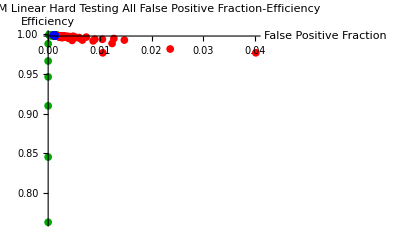

Show::gcomb: Could not combine the graphics objects in Show[SVMLinearSoftFPFNPlot, BDSLinearSoftFPFNPlot, BDTLinearSoftFPFNPlot, PlotRange → All].

Show[SVMLinearSoftFPFNPlot,BDSLinearSoftFPFNPlot,BDTLinearSoftFPFNPlot,PlotRange→All]

Show::gcomb: Could not combine the graphics objects in Show[SVMCircleHardFPFNPlot, BDSCircleHardFPFNPlot, BDTCircleHardFPFNPlot, PlotRange → All].

Show[SVMCircleHardFPFNPlot,BDSCircleHardFPFNPlot,BDTCircleHardFPFNPlot,PlotRange→All]

Show::gcomb: Could not combine the graphics objects in Show[SVMCircleSoftFPFNPlot, BDSCircleSoftFPFNPlot, BDTCircleSoftFPFNPlot, PlotRange → All].

Show[SVMCircleSoftFPFNPlot,BDSCircleSoftFPFNPlot,BDTCircleSoftFPFNPlot,PlotRange→All]

Show::gcomb: Could not combine the graphics objects in Show[SVMTwoCircleHardFPFNPlot, BDSTwoCircleHardFPFNPlot, BDTTwoCircleHardFPFNPlot, PlotRange → All].

Show[SVMTwoCircleHardFPFNPlot,BDSTwoCircleHardFPFNPlot,BDTTwoCircleHardFPFNPlot,PlotRange→All]

Show::gcomb: Could not combine the graphics objects in Show[SVMTwoCircleSoftFPFNPlot, BDSTwoCircleSoftFPFNPlot, BDTTwoCircleSoftFPFNPlot, PlotRange → All].

Show[SVMTwoCircleSoftFPFNPlot,BDSTwoCircleSoftFPFNPlot,BDTTwoCircleSoftFPFNPlot,PlotRange→All]

```mathematica
Show[SVMFPEPlot[SVMLinearHardTestingAllRawData, "Linear Hard Testing All"],BDSFPEPlot[BDSLinearHardTestingAllRawData, "Linear Hard Testing All"],BDTFPEPlot[BDTLinearHardTestingAllRawData, "Linear Hard Testing All"],PlotRange-> All]

Show[SVMLinearSoftFPFNPlot,BDSLinearSoftFPFNPlot,BDTLinearSoftFPFNPlot,PlotRange-> All]

Show[SVMCircleHardFPFNPlot,BDSCircleHardFPFNPlot,BDTCircleHardFPFNPlot,PlotRange-> All]
Show[SVMCircleSoftFPFNPlot,BDSCircleSoftFPFNPlot,BDTCircleSoftFPFNPlot,PlotRange-> All]

Show[SVMTwoCircleHardFPFNPlot,BDSTwoCircleHardFPFNPlot,BDTTwoCircleHardFPFNPlot,PlotRange-> All]
Show[SVMTwoCircleSoftFPFNPlot,BDSTwoCircleSoftFPFNPlot,BDTTwoCircleSoftFPFNPlot,PlotRange-> All]
```